# GWPNumerical Extension Package

Jeremy B. Maddox

Department of Chemistry and Biochemistry
Western Kentucky University
Bowling Green, KY 42101-1079
Email: jeremy.maddox@wku.edu

The GWPNumerical extension generalizes the GWPTools Mathematica package to arbitrary time-dependent quadratic potentials and non-stationary thermal environments across all pure-state (1D, 2D, SS1D, MC1D) and open-system (RDM1D) wavepacket engines. By exploiting the exact Gaussian structure of the wavepacket and reduced density matrix ansatzes, GWPNumerical replaces expensive spatiotemporal grid propagation with compact sets of ordinary differential equations (ODEs) solved via cached NDSolveValue routines. Unitary propagators directly integrate the coupled Riccati shape and continuous phase equations (automatically tracking unwrapped Maslov phases across caustics), while the open-system Caldeira–Leggett propagator utilizes a three-stage linear phase-space covariance pipeline that remains unconditionally stable across stiff mechanical and thermal ramps. Fully compatible with all existing GWPTools property queries and visualization tools, GWPNumerical provides both a high-precision benchmarking standard for quantum trajectory methods and a fast, interactive calculator for modeling pulsed laser control, multidimensional mode-mixing, and nonequilibrium quantum thermodynamics.

## Loading the Package

Rather than forcing every session to load all multidimensional, multi-component, and open-system numerical solvers at startup, the master orchestrator package GWPNumerical dynamically inspects which core GWPTools engines are currently active in the Wolfram session and selectively loads the corresponding numerical extensions, registering their “Numerical” (and “NumericalCL”) potential templates into GWPRegistry.

Because GWPNumerical checks the active context path at the moment it is called, any optional engines (2D, SS1D, MC1D, or RDM1D) should be loaded prior to calling GWPNumerical (note that GWPEngine1D is loaded automatically by the base GWPTools package).

Here is an example of initializing the complete suite of engines alongside the numerical extension:

```mathematica
Quit[]
```

```mathematica
PacletDirectoryLoad["/Users/jrm82302/maddox/Projects/Mathematica/GWPTools"];
Needs["MaddoxScience`GWPTools`"];
Needs["MaddoxScience`GWPTools`GWPEngine2D`"];
Needs["MaddoxScience`GWPTools`GWPEngineSS1D`"];
Needs["MaddoxScience`GWPTools`GWPEngineMC1D`"];
Needs["MaddoxScience`GWPTools`GWPEngineRDM1D`"];
Needs["MaddoxScience`GWPTools`GWPNumerical`"];
```

As detailed in the next section, GWPNumerical automatically caches the InterpolatingFunction solutions generated by NDSolveValue to accelerate repeated property queries. However, because this cache is indexed by the symbols passed into the “Potential” option, modifying a parameter inside a named potential function (such as changing a ramp rate or coupling constant within v2Ramp[t_]) will not automatically trigger a fresh integration if the function symbol itself remains unchanged.

Calling GWPClearCache[] strips all stored numerical trajectories from memory while preserving the underlying solver definitions, forcing NDSolveValue to re-integrate the equations of motion on the next query.  Use as needed if you wish to modify the Example Problems (below) that use parameterized functions.

## Software Architecture

### Function Slot Paradigm

GWPNumerical provides two new potential models.  “Numerical” is used to calculate the unitary evolution for a given wavepacket type.  “NumericalCL” is an additional model specifically for the RDM1D engine (reduced density matrix) and is used to calculate dissipative dynamics according to the Caldeira-Leggett master equation, which features a friction parameter γ_d and thermal energy  k_B T associated with a thermal bath.

IMPORTANT: In all “Numerical” and “NumericalCL” potential specifications, the quadratic potential coefficients and bath parameters are evaluated inside NDSolveValue as v0[t], v1[t], v2[t], gamma[t], and kT[t].  Therefore, every potential and bath argument passed to a numerical model must be a callable function of a single time argument (either a pure function using # and &, or the symbol name of a defined function).

#### Example 1: Using pure functions (with # and &)

This example shows the correct usage of pure functions where the potential coefficients are just simply constant values.

```mathematica
m=1;
omega=1;
tMin=0;
tMax=3*2*Pi;
obj=GWP["1D"]["Potential"->{"Numerical", 0 &, 0 &, (1/2 * m * omega^2) &,tMin,tMax}]
```

GWPObject[…]

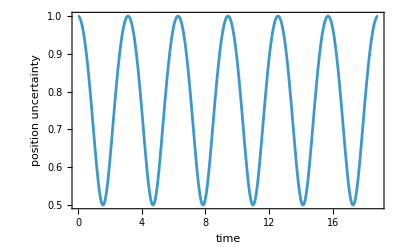

```mathematica
GraphicsRow[{
Plot3D[obj["PEX"][x,t],{t,tMin,tMax},{x,-3,3},AxesLabel->{"time","position","V(x,t)"},BaseStyle->FontSize->12],
Plot[obj["UX"][t],{t,tMin,tMax},Frame->True,FrameLabel->{"time","position uncertainty"},BaseStyle->FontSize->12]
}]
```

#### Example 2: Using function heads (symbol names)

This example illustrates using proper function symbols to specify the potential coefficients.

```mathematica
v0[t_]=0;
v1[t_]=0;
v2Ramp[t_] := 3/8 - 1/8 * Tanh[3 * (t - 4)];
tMin=0;
tMax=3*2*Pi;
Clear[obj]
obj=GWP["1D"]["Potential"->{"Numerical", v0, v1, v2Ramp, tMin, tMax}]
```

GWPObject[…]

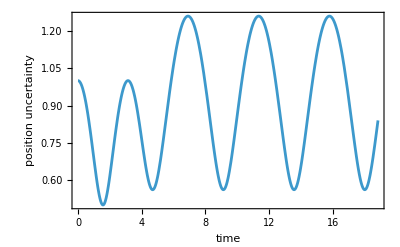

```mathematica
GraphicsRow[{
Plot3D[obj["PEX"][x,t],{t,tMin,tMax},{x,-3,3},AxesLabel->{"time","position","V(x,t)"},BaseStyle->FontSize->12],
Plot[obj["UX"][t],{t,tMin,tMax},Frame->True,FrameLabel->{"time","position uncertainty"},BaseStyle->FontSize->12]
}]
```

#### Example 3: Incorrect potential specification (raw numbers passed)

This illustrates incorrect usage where the potential parameters are not input using functions.

```mathematica
(* Incorrect usage of raw numbers *)
obj=GWP["1D"]["Potential"->{"Numerical", 0, 0, 1/2, 0, 10}]
```

GWPObject[…]

```mathematica
(* ERROR: 0[t] is not a number! *)
obj["PEX"][0,1]
```

Set::shape: Lists {MaddoxScience`GWPTools`GWPNumerical1D`Private`solRA$27891,MaddoxScience`GWPTools`GWPNumerical1D`Private`solIA$27891,MaddoxScience`GWPTools`GWPNumerical1D`Private`solX$27891,MaddoxScience`GWPTools`GWPNumerical1D`Private`solP$27891,MaddoxScience`GWPTools`GWPNumerical1D`Private`solRG$27891,MaddoxScience`GWPTools`GWPNumerical1D`Private`solIG$27891} and NDSolveValue[«1»] are not the same shape.

0[1]

In future versions, we will improve the code to also accept constants (i.e., not functions), but for now, they must be input as functions.

### Passing NDSolve Options

All numerical potential templates accept trailing opts___ that are forwarded directly to NDSolveValue. For long-time integrations, stiff dissipative ramps, or high-precision energy/Jarzynski work calculations, users can append standard NDSolve options directly inside the potential list:

```mathematica
obj1=GWP["1D"]["Potential"->{"Numerical" ,0&,0&,1/2&,0,2Pi}];
obj2=GWP["1D"]["Potential"->{"Numerical" ,0&,0&,1/2&,0,2Pi,WorkingPrecision->20}];
```

```mathematica
obj1["UX"][1]
obj2["UX"][1]
```

0.684796

0.6847955276318356728

Notice that the options go INSIDE the curly bracket for the “Potential” options.  If you put it outside, the option won’t get passed and unfortunately there is no warning at this time (I will get to fixing that...eventually).

```mathematica
obj3=GWP["1D"]["Potential"->{"Numerical" ,0&,0&,1/2&,0,2Pi},WorkingPrecision->20];
```

```mathematica
obj3["UX"][1]
```

0.684796

### NDSolveValue Memoization

In interactive workflows (Manipulate, Animate, or Plot over time), a wavepacket property may be queried thousands of times for the same potential and initial state. To prevent NDSolveValue from re-integrating the differential equations at every time point, each numerical package caches its InterpolatingFunction list using Mathematica’s downvalue memoization idiom.

```mathematica
obj=GWP["1D"]["Potential"->{"Numerical" ,0&,1/10&,1/2&,0,10}];
```

First query at t_1∈[t_min,t_max]: NDSolveValue integrates the ODEs across the full interval once and stores the resulting InterpolatingFunction objects in memory.

```mathematica
Timing[obj["UX"][1]]
```

{0.002286,0.684796}

Subsequent queries at t_2, t_3, …, etc.: The router retrieves the cached InterpolatingFunctions and evaluates them at those time values.

```mathematica
Timing[obj["UX"][2]]
```

{0.000415,0.616347}

Notice the second evaluation was an order of magnitude faster.

Domain bounds protection: Querying any numerical model at t<t_min or t>t_max triggers the out of bounds message and safely aborts evaluation ($Failed) rather than extrapolating outside the integration window:

```mathematica
obj["UX"][11]
```

MaddoxScience`GWPTools`GWPDeveloper`GWP1DNUMERICAL::outofbounds: The requested time 11 is outside the simulated time domain [0, 10].

MaddoxScience`GWPTools`GWPDeveloper`GWP1DUX[$Failed]

### Clearing the Memoization Cache (GWPClearCache)

Because memoized InterpolatingFunction objects persist in the kernel session’s DownValues, two situations call for explicitly flushing the cache:

Memory reclamation after large parameter sweeps or high-precision runs.

In-place redefinition of named coefficient functions: When potential coefficients are passed as named functions (e.g., v1), the cache keys on the symbol v1 itself. Redefining v1[t_] in-place does not change the symbol name inside obj, so calling GWPClearCache[] is required to force NDSolveValue to re-integrate with the updated potential.

```mathematica
(*1. Define a numerical wavepacket using a named linear driving coefficient v1[t]*)
GWPClearCache["Quiet"];
v1[t_]:=1/10;
objNamed=GWP["1D"]["Potential"->{"Numerical",0&,v1,1/2&,0,10}];
```

```mathematica
(*First evaluation integrates the ODEs and caches the result for v1[t]=1/10*)
Timing[objNamed["RX"][2]]
```

{0.002537,-0.141615}

```mathematica
(*Subsequent evaluation hits the cache (fast)*)
Timing[objNamed["RX"][2]]
```

{0.000357,-0.141615}

```mathematica
(*2. Redefine v1[t] in-place to a stronger driving force*)
v1[t_]:=1/2;
(*Without clearing the cache,objNamed still returns the old cached trajectory!*)
objNamed["RX"][2]
```

-0.141615

```mathematica
(*3. Flush all memoized NDSolve caches across GWPNumerical*)
GWPClearCache[]
```

[GWPNumerical] Cleared caches: {GWP1DNDSolveCache,GWP2DNDSolveCache,GWPMC1DNDSolveCache,GWPRDM1DNDSolveCache,GWPSS1DNDSolveCache}

```mathematica
(*Now objNamed re-integrates the ODEs (note the integration timing) and reflects v1[t]=1/2*)Timing[objNamed["RX"][2]]
```

{0.002565,-0.708073}

```mathematica
(* Subsequent evaluations with the new v1 use the cached solutions *)
Timing[objNamed["RX"][2]]
```

{0.000398,-0.708073}

## Example Problems

### 1D Squeezed-State Benchmark Across All Six Parameters

In this example, we validate the six-equation 1D numerical solver against the exact analytical harmonic oscillator for a non-stationary squeezed and displaced GWP.  We will compare the time-dependent residual errors across all six real wavepacket parameters using default machine precision versus 30-digit arbitrary precision.

To rigorously test all six coupled equations of motion in GWPNumerical1D, we initialize a non-stationary GWP with a squeezed and chirped complex width parameter (α_0=3/2+ⅈ/2) and a displaced phase-space center (x_0=1, p_0=1/2, and γ_0=0) over five full harmonic periods t ∈[0,10π].

```mathematica
(* Parameters *)
omega0=1;
tMin=0;
tMax=5*2*Pi;
(*Squeezed+chirped shape and displaced phase-space center*)
a0=3/2+I/2;
x0=1;
p0=1/2;
g0=0;
(*Static quadratic coefficient V2(t)=(1/2) m omega0^2*)
v0=0&;
v1=0&;
v2Static=(1/2*omega0^2)&;
(*Constuct GWPs*)
objExact=GWP["1D"][a0,x0,p0,g0,"Potential"->{"Harmonic",omega0}];
objNumMach=GWP["1D"][a0,x0,p0,g0,"Potential"->{"Numerical",v0,v1,v2Static,tMin,tMax}];
objNumPrec30=GWP["1D"][a0,x0,p0,g0,"Potential"->{"Numerical",v0,v1,v2Static,tMin,tMax,WorkingPrecision->30}];
```

Each of the six real dynamical parameters exhibits a distinct physical signature across the five-period window.  Governed by Ehrenfest’s theorem, the position and momentum centers execute simple harmonic motion at the fundamental trap frequency. Because the initial shape parameter does not match the stationary ground-state width, the wavepacket undergoes periodic spatial “breathing.” The real part oscillates strictly positively between its compressed and expanded turning points at twice the trap frequency. Simultaneously, the phase-chirp parameter oscillates between positive and negative values at twice the frequency, passing through zero precisely at the inner and outer turning points of real part, where the wavepacket is momentarily unchirped. The real phase accumulates a negative drift modulated by fast oscillatory ripples at twice the trap frequency arising from the alternating kinetic and potential energy of the classical Lagrangian.  The imaginary part of the phase oscillates periodically in lockstep with the real shape parameter to preserve the wavepacket norm, and in this case returns exactly to zero at the end of every breathing cycle.

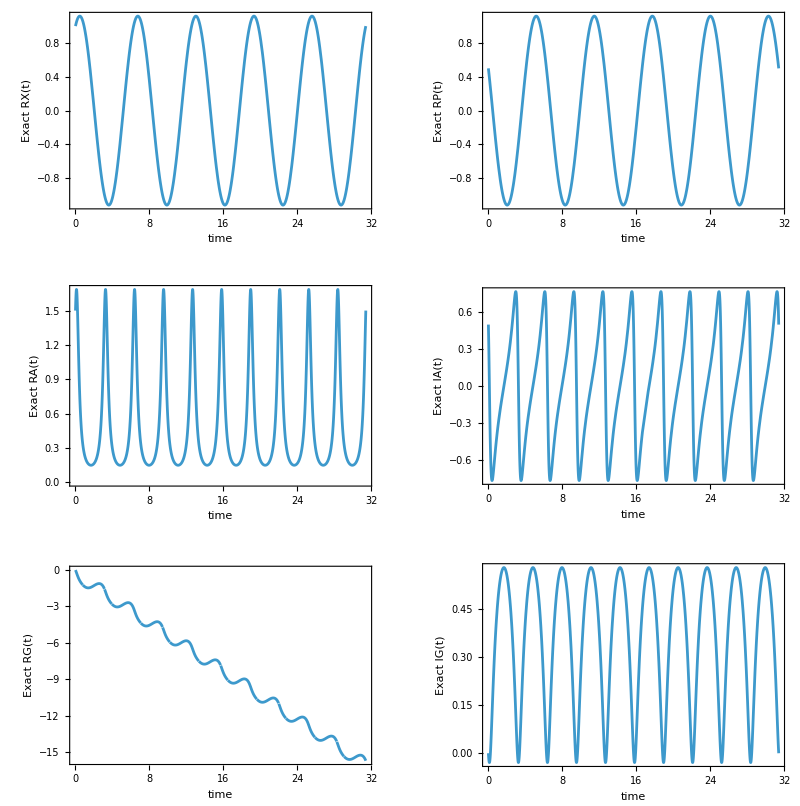

```mathematica
opts={Frame->True,BaseStyle->FontSize->12};
GraphicsGrid[{
{Plot[objExact["RX"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact RX(t)"}],
Plot[objExact["RP"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact RP(t)"}]},
{Plot[objExact["RA"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact RA(t)"}],
Plot[objExact["IA"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact IA(t)"}]},
{Plot[objExact["RG"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact RG(t)"}],
Plot[objExact["IG"][t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","Exact IG(t)"}]}
}]
```

The following functions calculate the absolute residual error of the numerical wavepacket’s parameters as a function of time, which are then plotted below.  Comparing the exact analytical solution against the numerical integrator over five harmonic periods reveals a clear hierarchy in how numerical truncation errors accumulate across the six wavepacket parameters, while demonstrating a dramatic six-to-seven order-of-magnitude accuracy improvement when increasing the working precision to thirty digits. Because the classical position and momentum centers obey smooth, strictly linear equations of motion, they exhibit the smallest overall residuals—fluctuating without a net upward trend in machine precision while showing only a tiny, steady phase drift at high precision. By contrast, the real width and imaginary chirp parameters are governed by coupled, nonlinear equations that oscillate at twice the trap frequency, causing their residuals to set the dominant error scale and grow steadily over time in both precision regimes. Finally, because the global action phase and normalization parameters directly integrate the width and chirp over time, their errors grow in lockstep with the shape parameters. Together, these trends offer rich opportunities for deeper numerical exploration—such as benchmarking symplectic and implicit Runge–Kutta integration schemes, investigating long-time secular phase drift, and analyzing how adaptive step-size controllers couple linear and nonlinear subsystems.

```mathematica
(* Define absolute residual functions for each of the six parameters *)errRA[t_]:={Abs[objExact["RA"][t]-objNumMach["RA"][t]],Abs[objExact["RA"][t]-objNumPrec30["RA"][t]]};
errIA[t_]:={Abs[objExact["IA"][t]-objNumMach["IA"][t]],Abs[objExact["IA"][t]-objNumPrec30["IA"][t]]};
errRX[t_]:={Abs[objExact["RX"][t]-objNumMach["RX"][t]],Abs[objExact["RX"][t]-objNumPrec30["RX"][t]]};
errRP[t_]:={Abs[objExact["RP"][t]-objNumMach["RP"][t]],Abs[objExact["RP"][t]-objNumPrec30["RP"][t]]};
errRG[t_]:={Abs[objExact["RG"][t]-objNumMach["RG"][t]],Abs[objExact["RG"][t]-objNumPrec30["RG"][t]]};
errIG[t_]:={Abs[objExact["IG"][t]-objNumMach["IG"][t]],Abs[objExact["IG"][t]-objNumPrec30["IG"][t]]};
```

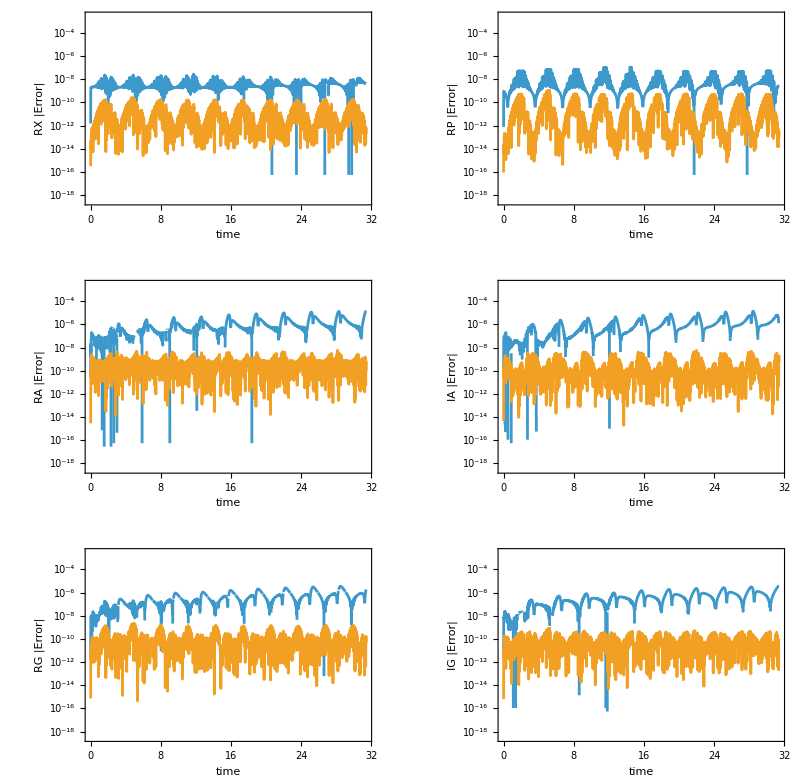

```mathematica
opts={PlotRange->{3*10^-19,0.003},Frame->True,BaseStyle->FontSize->12};
GraphicsGrid[{
{LogPlot[Evaluate@errRX[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RX |Error|"}],
LogPlot[Evaluate@errRP[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RP |Error|"}]},
{LogPlot[Evaluate@errRA[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RA |Error|"}],
LogPlot[Evaluate@errIA[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","IA |Error|"}]},
{LogPlot[Evaluate@errRG[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RG |Error|"}],
LogPlot[Evaluate@errIG[t],{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","IG |Error|"}]}
}]
```

### 1D Paul Trap & Parametric Phase-Space Squeezing

In this example, we simulate a coherent GWP in a parametrically modulated harmonic trap with time-dependent curvature

V_2(t)=1/2 m ω_0^2(1+ϵ s(t)sin(Ω t))

where ω_0 is the unperturbed trap frequency, ϵ is the modulation depth, Ω is the drive frequency, and s(t) is a dimensionless switching envelope.  We compare three distinct physical driving protocols:

(1) Sudden Resonant Modulation (Ω=2 ω_0, s(t)=1): The modulation is active at full amplitude from t=0.  Although the potential curvature starts at its unperturbed baseline V_2(0)=1/2 m ω_0^2, its initial time derivative is discontinuous ((V̇)_2(0)!=0), imparting an immediate parametric impulse at t=0.

(2) Smooth Resonant Turn-On (Ω=2 ω_0, s(t) = 1/2(1+tanh(κ(t-t_0))): The modulation ramps up smoothly from zero around t_0=2π (with switching rate κ=4/5), allowing the wavepacket to execute one full unperturbed oscillation before the drive engages.  Because the envelop s(t) breaks strict time-periodicity during the ramp, closed-form Mathieu or Floquet analytical solutions no longer apply, necessitating numerical integration.

(3) Smooth Off-Resonant Paul Trap Regime (Ω=6 ω_0, with the same ramp): Using the same smooth turn-on envelope, the trap is driven well above the fundamental parametric resonance. Operating in this stable Paul-trap regime avoids exponential parametric amplification, yielding bounded secular confinement dressed by high-frequency motion.

```mathematica
(*Parameters*)
omega0=1;
eps=3/10;
kappa=4/5;
t0=2*Pi;
tMin=0;
tMax=3*2*Pi;
(*1. Sudden Resonant Drive (Omega=2*omega0)*)
v2ResSudden[t_]:=(1/2)*omega0^2*(1+eps*Sin[2*omega0*t]);
(*2. Smooth Resonant Drive (Omega=2*omega0,centered at t0=2*Pi)*)
env[t_]:=(1/2)*(1+Tanh[kappa*(t-t0)]);
v2ResSmooth[t_]:=(1/2)*omega0^2*(1+eps*env[t]*Sin[2*omega0*t]);
(*3. Smooth Off-Resonant Paul Trap Drive (Omega=6*omega0)*)
v2OffResSmooth[t_]:=(1/2)*omega0^2*(1+eps*env[t]*Sin[6*omega0*t]);
(*Initialize displaced coherent-state wavepackets (alpha0=1/2,x0=1)*)
objResSudden=GWP["1D"][1/2,1,0,0,"Potential"->{"Numerical",0&,0&,v2ResSudden,tMin,tMax}];
objResSmooth=GWP["1D"][1/2,1,0,0,"Potential"->{"Numerical",0&,0&,v2ResSmooth,tMin,tMax}];
objOffResSmooth=GWP["1D"][1/2,1,0,0,"Potential"->{"Numerical",0&,0&,v2OffResSmooth,tMin,tMax}];
```

The figure below compares the time evolution of the quadratic curvature coefficient V_2(t) across the three protocols. Notice that the smooth resonant ramp remains nearly flat at the unperturbed value V_2=m ω_0/2=1/2 during the first trap half-period (t≲π) and smoothly locks onto the sudden resonant curve for t≳3, whereas the off-resonant ramp oscillates at three times the frequency within the same switching envelope.

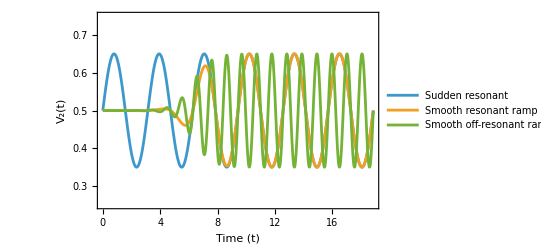

```mathematica
Plot[{v2ResSudden[t],v2ResSmooth[t],v2OffResSmooth[t]},{t,tMin,tMax},PlotRange->{1/4,3/4},Frame->True,FrameLabel->{"Time (t)","V_2(t)"},BaseStyle->{FontSize->12},PlotLegends->{"Sudden resonant","Smooth resonant ramp","Smooth off-resonant ramp"}]
```

Modulating a harmonic trap at twice its natural frequency (Ω=2 ω_0) places the oscillator inside the principal parametric resonance regime of the Mathieu equation, pumping mechanical energy continuously into both the classical trajectory and the quantum width oscillations. In the figure below, the classical position center x_t and momentum center p_t under the sudden and smooth resonant drives undergo exponential parametric amplification, whereas the off-resonant Paul-trap drive (Ω=6 ω_0) preserves stable, bounded harmonic oscillations dressed by faint high-frequency micromotion.

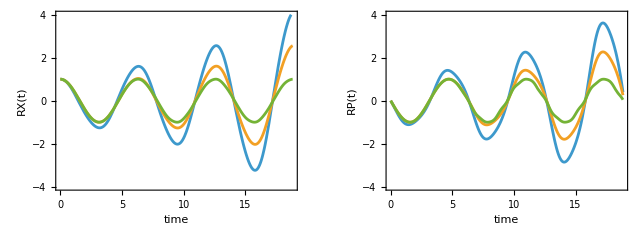

```mathematica
opts={PlotRange->{-4,4},Frame->True,BaseStyle->FontSize->12};
GraphicsRow[{
Plot[{objResSudden["RX"][t],objResSmooth["RX"][t],objOffResSmooth["RX"][t]},{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RX(t)"}],
Plot[{objResSudden["RP"][t],objResSmooth["RP"][t],objOffResSmooth["RP"][t]},{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","RP(t)"}]
}]
```

Turning to the quantum shape dynamics, the three driving protocols produce markedly different behavior in the position uncertainty Δ x_t and momentum uncertainty Δ p_t.

Sudden Resonant Squeezing: The discontinuous turn-on slope (V̇)_2(0)!=0 at t=0 immediately initiates parametric squeezing, causing Δ x_t and Δ p_t to oscillate π out of phase with exponentially growing envelopes that periodically compress below the unperturbed coherent ground-state limit Δ x_0=Δ p_0=1/√2.

Smooth Resonant Turn-On: Because the modulation envelope ramps up gradually around t_0=2π, the initial coherent state remains completely stationary throughout the quiet pre-ramp window (t≲π) before smoothly locking into exponential squeezing with a delayed phase relative to the sudden protocol.

Off-Resonant Paul-Trap Stability: Shifting the drive frequency to Ω=6 ω_0 moves the wavepacket outside the parametric instability regime. Rapid curvature modulations average out, leaving the spatial and momentum widths nearly constant aside from small, high-frequency ripples once the envelope turns on.

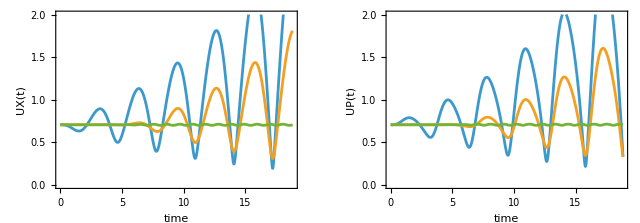

```mathematica
opts={Frame->True,BaseStyle->FontSize->12,PlotRange->{0,2}};
GraphicsRow[{
Plot[{objResSudden["UX"][t],objResSmooth["UX"][t],objOffResSmooth["UX"][t]},{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","UX(t)"}],
Plot[{objResSudden["UP"][t],objResSmooth["UP"][t],objOffResSmooth["UP"][t]},{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","UP(t)"}]
}]
```

At first glance, the rapid growth of the envelope of Δ x_t Δ p_t during resonant squeezing might suggest that the wavepacket is losing purity or undergoing effective heating. However, examining the symmetrized position–momentum covariance COVXP(t) alongside the Robertson–Schrödinger generalized uncertainty invariant,

det Σ(t)=(Δ x_t)^2(Δ p_t)^2-(Cov(x,p))_t^2=ℏ^2/4

reveals the underlying geometric mechanism. Whenever the squeezed wavepacket stretches between its turning points, strong position–momentum correlations (COVXP(t)) build up as the phase-space uncertainty ellipse tilts diagonally in the x p-plane.  As shown in the final pair of plots below, this growth in second term exactly compensates the first term, keeping the generalized uncertainty determinant locked at the minimum pure-state value of 1/4 across all three protocols. In accordance with Liouville’s theorem for unitary Gaussian evolution, parametric driving stretches and rotates the phase-space ellipse without altering its area—distinguishing coherent unitary squeezing from dissipative thermal broadening.

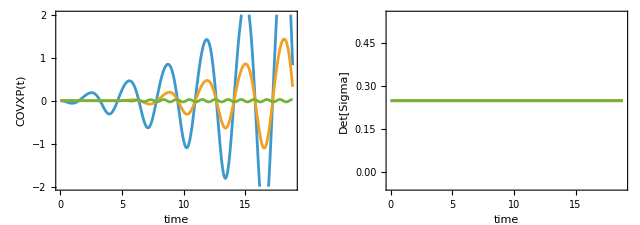

```mathematica
(*Robertson-Schrodinger Generalized Uncertainty Invariant:UX^2*UP^2-COVXP^2*)rsInvariant[obj_,t_]:=obj["UX"][t]^2*obj["UP"][t]^2-obj["COVXP"][t]^2;

GraphicsRow[{Plot[{objResSudden["COVXP"][t],objResSmooth["COVXP"][t],objOffResSmooth["COVXP"][t]},{t,tMin,tMax},Evaluate@opts,FrameLabel->{"time","COVXP(t)"},PlotRange->{-2,2}],Plot[{rsInvariant[objResSudden,t],rsInvariant[objResSmooth,t],rsInvariant[objOffResSmooth,t]},{t,tMin,tMax},PlotRange->{-0.05,0.55},Evaluate@opts,FrameLabel->{"time","Det[Sigma]"}]}]
```

### 1D Driven Multi-State Superpositions & Quantum Interference

In this example, we propagate a two-component Schrödinger cat state (SS1D) and a three-component coherent wavepacket train (MC1D) in a harmonic trap (ω_0=1) subjected to a transient, Gaussian-envelope dipole laser pulse:

V_1(t)=-F_0 ⅇ^(-1/τ^2(t-t_p)^2)cos(ω_d t)

where F_0 is the peak field amplitude, t_p is the pulse center time, τ is the pulse duration, and ω_d is the carrier frequency.

In the code below, we define and plot the time-dependent driving potential coefficient:

```mathematica
(*External Gaussian-envelope dipole driving field V1(t)*)
tMin=0;
tMax=20;
f0=4/5;
tp=6;
tau=2;
omegaD=1;
v1Pulse[t_]:=-f0*Exp[-(t-tp)^2/tau^2]*Cos[omegaD*t];
v2Trap=(1/2)&;
```

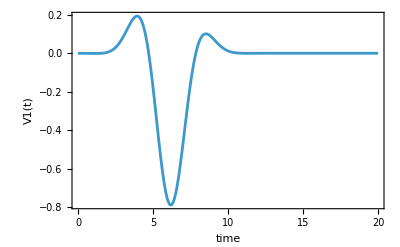

```mathematica
(*Visualize the transient dipole driving pulse V1(t)*)
Plot[v1Pulse[t],{t,tMin,tMax},PlotRange->All,Frame->True,FrameLabel->{"time","V1(t)"},BaseStyle->FontSize->12]
```

Next we define the superposition states.  For SS1D and MC1D, the initial wavepacket parameters are passed as component lists {A10, A20, ...}, {X10, X20, ...}, {P10, P20, ...}, {G10, G20, ...} along with the superposition weight option “C”:

SS1D Two-State Cat Superposition: Specialized for N=2 states and parameterized by a single relative mixing coefficient (where “C” -> 1 creates an equal-weight symmetric cat state). Here, the two branches are initialized as displaced coherent states (α_0=1/2 at x_0=±2).

MC1D Multi-Component Wavepacket Train: Supports an arbitrary number of basis states N and accepts a list of unnormalized mixing coefficients “C” -> {c1, c2, ...}. Here, three compressed Gaussian branches (α_0=1) are initialized at x_0∈{-5/2,0, 5/2}.

```mathematica
(*Two-State Schrödinger Cat State (SS1D)*)
catSS1D=GWP["SS1D"][{1/2,1/2},{-2,2},{0,0},{0,0},"C"->1,"Potential"->{"Numerical",0&,v1Pulse,v2Trap,tMin,tMax}];
(*Three-State Coherent Wavepacket Train (MC1D)*)
trainMC1D=GWP["MC1D"][{1,1,1},{-5/2,0,5/2},{0,0,0},{0,0,0},"C"->{1,1,1},"Potential"->{"Numerical",0&,v1Pulse,v2Trap,tMin,tMax}];
```

Both GWPNumericalSS1D and GWPNumericalMC1D integrate the 6N pure-state ODEs in a single cached NDSolveValue call and algebraically reconstruct all N(N-1)/2 off-diagonal interference cross-terms on the fly at time t via GWP1DPARAM12. Pre-binding the “RHOX” pure functions outside DensityPlot avoids repeated registry lookups across the plotting grid:

```mathematica
(*Pre-bind the density functions once outside the plot loop*)
rhoCat=catSS1D["RHOX"];
rhoTrain=trainMC1D["RHOX"];
opts={PlotPoints->60,PlotRange->Automatic,FrameLabel->{"time","position"},BaseStyle->FontSize->12};
GraphicsRow[{
DensityPlot[Chop@rhoCat[x,t],{t,tMin,tMax},{x,-5,5},Evaluate@opts],
DensityPlot[Chop@rhoTrain[x,t],{t,tMin,tMax},{x,-6,6},Evaluate@opts]
}]
```

-Graphics-

The space-time probability density plots (above) illustrate how macroscopic quantum superpositions respond to a resonant dipole pulse (ω_d=ω_0=1) centered at t_p=6. 

Prior to the laser pulse t≲4, the wavepacket branches oscillate symmetrically about the trap center.  Every half-period, the counter-propagating branches cross at the origin, producing sharp interference fringes whose spatial wavelength is set by the relative momentum at the collision point. 

As the resonant pulse peaks around t_p=6, it imparts a coherent momentum kick to the entire superposition. In accordance with the generalized Kohn theorem for quadratic potentials, a spatially uniform linear drive V_1(t) couples exclusively to the center-of-mass coordinate: for t>6, the entire interference pattern sweeps back and forth in large-amplitude collective oscillations without altering the relative phase-space separation or collision timing between the individual branches.

In the two-state cat superposition (SS1D), the stationary-width branches α_0=1/2 maintain a constant envelope width while sweeping back and forth across the trap with periodic two-beam interference nodes at the turning points of their relative motion. In the three-state wavepacket train (MC1D), initializing compressed branches (α_0=1) introduces simultaneous width breathing at 2 ω_0 alongside three-wavepacket focal collisions.  At each collision, three pairwise momentum differences (Δp_12, Δp_23, Δ p_13=2 Δ p_12) superpose with the breathing envelopes to weave a rich, multi-scale interference pattern along the driven center-of-mass trajectory.

### 2D Time-Dependent Mode Mixing

In this example, we model transient intramolecular vibrational energy redistribution (IVR) and coherent mode swapping in a two-dimensional harmonic potential. A 2D GWP—initially displaced and squeezed solely along the x-coordinate while sitting in its uncoupled ground state along y—is subjected to a smoothly windowed bilinear coupling V_11(t) x y

V_11(t)=1/2 κ_xy(tanh(t-t_1)-tanh(t-t_2))

which temporarily hybridizes the two orthogonal oscillators during the interval t_1≲t≲t_2, rotating the 2×2 complex shape matrix A_t and transferring both classical momentum and quantum squeezing into the y-mode.

First, we define the coupling window and initialize the 2D wavepacket. Notice that for GWP[“2D”], the “Numerical” potential template takes six callable coefficient functions corresponding to the 2D Taylor expansion {V_00,V_10,V_01,V_20,V_02,V_11}:

```mathematica
(*Parameters*)
tMin=-20;
tMax=50;
(*Uncoupled degenerate harmonic frequencies:omegaX=omegaY=1->V20=V02=1/2*)
v00=0&;
v10=0&;
v01=0&;
v20Func=(1/2)&;
v02Func=(1/2)&;
(*Smoothly switch on bilinear xy coupling V11(t) between t1=5 and t2=20*)
t1=5;
t2=20;
kappaXY=35/100;
v11Window[t_]:=kappaXY*(1/2)*(Tanh[t-t1]-Tanh[t-t2]);
(*Initial shape matrix: squeezed along x,ground state along y*)
aMat0={{1,0},{0,1/2}};
r0={3/2,0};
p0={0,0};
(* Initialize the wavepacket *)
psi2D=GWP["2D"][aMat0,r0,p0,0,"Potential"->{"Numerical",v00,v10,v01,v20Func,v02Func,v11Window,tMin,tMax}];
```

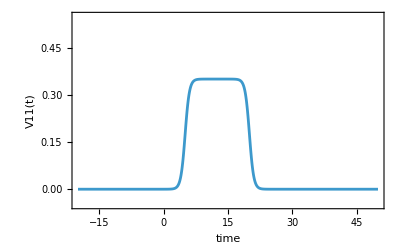

```mathematica
(*Visualize the bilinear mode-coupling window V11(t)*)
Plot[v11Window[t],{t,tMin,tMax},PlotRange->{-0.05,0.55},Frame->True,FrameLabel->{"time","V11(t)"},BaseStyle->FontSize->12]
```

Comparing the classical trajectory centers alongside the second-moment spatial uncertainties highlights the three distinct stages of the protocol:

Stage (1) Uncoupled Pre-Window Evolution (-20<=t≲5): Prior to the coupling ramp, the two coordinates are dynamically independent. The classical center oscillates purely along the x-axis while y_t=0 remains completely quiescent. Simultaneously, the compressed x-width breathes at twice the trap frequency 2 ω_0, the y-width remains flat at its coherent ground-state value, and the cross-mode spatial covariance vanishes identically.

Stage (2) Active Hybridization and Elliptical Rotation (5<t≲ 20): As V_11(t) ramps onto its plateau κ_xy=35/100, the degenerate x and y oscillators hybridize into symmetric and antisymmetric normal modes (x±y) with split frequencies

ω_±=√(ω_0^2±κ_(x y))

This frequency splitting induces coherent Rabi-like normal-mode beating at the difference frequency Δω=ω_+-ω_-, transferring classical oscillation amplitude from x_t into y_t.  At the quantum level, the off-diagonal shape matrix element α_(x y,t) becomes non-zero, rotating the 2D Gaussian uncertainty ellipse in the x y-plane, generating strong inter-mode spatial correlations, and transferring parametric width breathing from the x-mode into the y-mode.

Stage (3) Post-Window State Lock-In (t≳20): Once the coupling window smoothly turns off after t_2=20, the off-diagonal coupling vanishes (α_(xy,t) decouples in the Hamiltonian) and inter-mode energy exchange ceases. Both oscillators remain locked in their newly established classical amplitudes and correlated breathing states—realizing a controllable phonon beam-splitter or mode-swap gate in a 2D ion or optical trap.

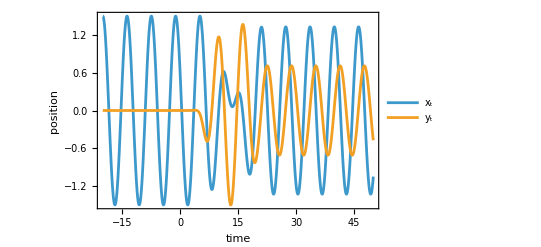

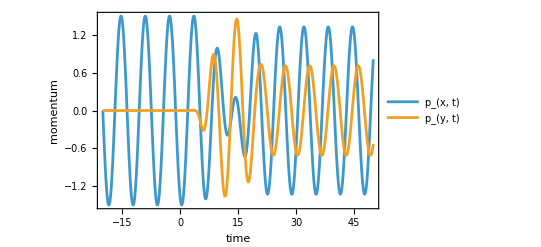

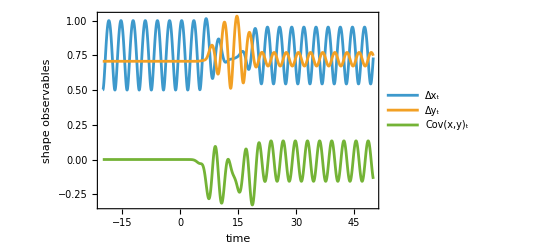

```mathematica
opts={Frame->True,BaseStyle->FontSize->12};
Plot[{
psi2D["PositionCenterX"][t],
psi2D["PositionCenterY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"x_t","y_t"},FrameLabel->{"time","position"}]
Plot[{
psi2D["MomentumCenterX"][t],
psi2D["MomentumCenterY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"p_(x, t)","p_(y, t)"},FrameLabel->{"time","momentum"}]
Plot[{
psi2D["PositionUncertaintyX"][t],
psi2D["PositionUncertaintyY"][t],
psi2D["PositionCovarianceXY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"Δx_t","Δy_t","Cov(x,y)_t"},FrameLabel->{"time","shape observables"}]
```

### Nonequilibrium Quantum Thermodynamics

To demonstrate open-system quantum dynamics beyond pure-state wavepackets, this example evolves a one-dimensional Gaussian reduced density matrix coupled to an Ohmic thermal reservoir via the Caldeira–Leggett master equation. Unlike a pure Gaussian state—whose spatial width and momentum spread are rigidly locked together—a mixed Gaussian density matrix incorporates an independent real decoherence parameter θ_t>0 that suppresses spatial coherence.

Note that in the following, subscript i denotes initial thermodynamic state while f denotes the final thermodynamic state.

We initialize the system in an exact stationary thermal Gibbs state at t=0 corresponding to a weak harmonic trap ω_i=1/2 and a cold, weakly coupled bath (γ_(d,i)=3/20, k_B T_i=4/5). Around t_0=10, the trap curvature V_2(t), friction coefficient γ_d(t), and bath temperature k_B T(t) are simultaneously ramped via smooth hyperbolic-tangent switching functions to a stiffer, hotter target regime (ω_f=1, γ_(d,f)=1/4, k_B T_f=8/5), i.e., work will be done on the system under non-isothermal conditions.  Because all three control functions vary simultaneously over a finite switching window, the coupled nonlinear differential equations for the density matrix parameters admit no closed-form analytical solution, providing a stringent benchmark for the numerical open-system propagator.

First, we define the initial and final thermodynamic state parameters using natural units (ℏ=1 and m=1), along with the asymptotic equilibrium parameters:

```mathematica
(* Natural units *)
hbar=1;
m=1;
(*Initial Thermodynamic State Parameters (t=0)*)
omegaI=1/2;
gammaI=3/20;
kTI=4/5;
(*Final Target Thermodynamic State Parameters (t->tMax)*)
omegaF=1;
gammaF=1/4;
kTF=8/5;
(*Exact Stationary Thermal Equilibrium Parameters at t=0*)
a0Eq=(m*omegaI^2)/(4*kTI);
x0Eq=0;
p0Eq=0;
g0Eq=(1/4)*Log[(2*a0Eq)/Pi];
theta0Eq=(m*kTI)/(2*hbar^2)-(m*omegaI^2)/(8*kTI);
(*Exact Target Asymptotic Equilibrium Values for Comparison*)
aFinalEq=(m*omegaF^2)/(4*kTF);
thetaFinalEq=(m*kTF)/(2*hbar^2)-(m*omegaF^2)/(8*kTF);
```

Next, we introduce smooth initial-to-final state transition ramps. We hold the system in its initial equilibrium until t_0=10, then smoothly ramp V_2(t), γ_d(t), and k_B T(t) to their new values at steepness κ=1. For comparison, we also construct a unitary (γ_d= 0) counterpart subjected to the same mechanical trap ramp V_2(t).

```mathematica
(* Time parameters *)
tMin=0;
tMax=50;
t0=10;
kappa=1;
(*Helper for smooth Tanh switching between valI and valF at t=t0*)
smoothRamp[valI_,valF_,t_]:=(valI+valF)/2+((valF-valI)/2)*Tanh[kappa*(t-t0)];
(*Time-dependent Potential Curvature V2(t)=1/2 m omega(t)^2,Damping,and Bath Temperature*)
v2Ramp[t_]:=(1/2)*m*smoothRamp[omegaI^2,omegaF^2,t];
gammaRamp[t_]:=smoothRamp[gammaI,gammaF,t];
kTRamp[t_]:=smoothRamp[kTI,kTF,t];
```

Here is a plot of the ramping functions:

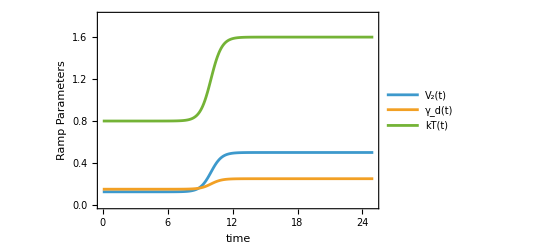

```mathematica
Plot[{v2Ramp[t],gammaRamp[t],kTRamp[t]},{t,tMin,tMax/2},PlotRange->{0,1.8},Frame->True,FrameLabel->{"time","Ramp Parameters"},BaseStyle->FontSize->12,PlotLegends->{"V_2(t)","γ_d(t)","kT(t)"}]
```

The following constructs the two GWPs for the dissipative and unitary dynamics:

```mathematica
(*Open-System Caldeira-Leggett Evolution ("NumericalCL")*)
rdmCL=GWP["RDM1D"][a0Eq,x0Eq,p0Eq,g0Eq,theta0Eq,"Potential"->{"NumericalCL",0&,0&,v2Ramp,gammaRamp,kTRamp,tMin,tMax,AccuracyGoal->12,PrecisionGoal->12,MaxSteps->Infinity},"HBAR"->hbar,"MASS"->m];
(*Isolated Unitary Evolution ("Numerical") from the Same Initial Thermal State*)
rdmUnitary=GWP["RDM1D"][a0Eq,x0Eq,p0Eq,g0Eq,theta0Eq,"Potential"->{"Numerical",0&,0&,v2Ramp,tMin,tMax,AccuracyGoal->12,PrecisionGoal->12,MaxSteps->Infinity},"HBAR"->hbar,"MASS"->m];
```

Comparing the open-system trajectory (“NumericalCL”, solid blue curve) against an otherwise identical isolated evolution (“Numerical”, solid orange curve) highlights the distinct physical roles of mechanical driving and environmental dissipation. Prior to the switching window (0<t≲7), both systems remain stationary at the initial equilibrium shape and decoherence parameters.

As the trap stiffens around t_0=10, mechanical work is injected into the oscillator. In the isolated unitary system, this injected energy cannot be dissipated; the wavepacket is permanently excited into undamped parametric breathing oscillations while its quantum purity (as shown in later results) remains frozen.  Conversely, in the dissipative system, environmental friction dampens the transient breathing oscillations within a few relaxation times τ_rel~γ_f^-1 guiding both the real shape parameter and the decoherence smoothly onto their new asymptotic equilibrium plateaus.

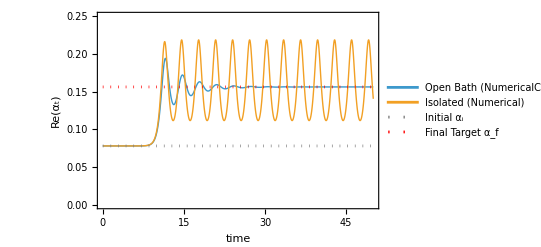

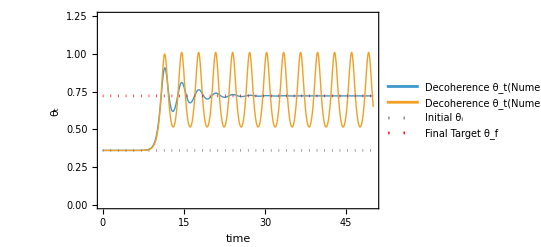

```mathematica
(*Spatial Width Parameter Re[alpha(t)]:Unitary Breathing vs.Thermal Equilibration*)
Plot[{
rdmCL["RealShape"][t],
rdmUnitary["RealShape"][t],
a0Eq,aFinalEq},{t,tMin,tMax},PlotRange->{0,.25},PlotStyle->{Thick,Thick,{Dotted,Gray},{Dotted,Red}},PlotLegends->{"Open Bath (NumericalCL)","Isolated (Numerical)","Initial α_i","Final Target α_f"},Frame->True,FrameLabel->{"time","Re(α_t)"},BaseStyle->FontSize->12]

(*Thermal Decoherence Parameter theta(t) Transition to New Equilibrium*)
Plot[{
rdmCL["Decoherence"][t],
rdmUnitary["Decoherence"][t],
theta0Eq,thetaFinalEq},{t,tMin,tMax},PlotRange->{0,1.25},PlotStyle->{Thick,Thick,{Dotted,Gray},{Dotted,Red}},PlotLegends->{"Decoherence θ_t(NumericalCL)","Decoherence θ_t(Numerical)","Initial θ_i","Final Target θ_f"},Frame->True,FrameLabel->{"time","θ_t"},BaseStyle->FontSize->12]
```

The diagonal population density snapshots at t = 0 (initial), 12 (midway), and 50 (final) illustrate a counterintuitive thermodynamic interplay between mechanical confinement and thermal heating. Although the bath temperature doubles during the ramp (T_f/T_i=2)—which by itself would thermally broaden the position distribution—the trap frequency simultaneously doubles, quadrupling the restoring curvature (ω_f^2/ω_i^2=4). Because the equilibrium inverse spatial variance scales as

Re(α_eq)= (m ω^2)/(4 k_B T)

the four-fold stiffening overcomes the two-fold heating, doubling Re(α_eq) and compressing the final equilibrium spatial density by a net factor of √2 relative to the initial state.

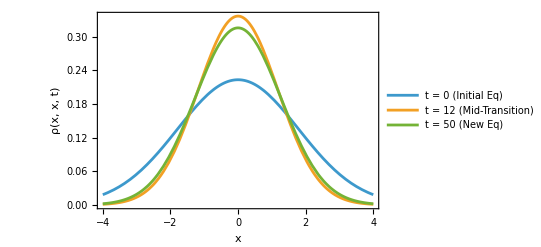

```mathematica
(*3. Visualize Diagonal Spatial Probability Density rho(x,x,t) Before vs.After Equilibration*)
Plot[{rdmCL["DensityX"][x,0],rdmCL["DensityX"][x,12],rdmCL["DensityX"][x,tMax]},{x,-4,4},PlotLegends->{"t = 0 (Initial Eq)","t = 12 (Mid-Transition)","t = 50 (New Eq)"},Frame->True,FrameLabel->{"x","ρ(x, x, t)"},BaseStyle->FontSize->12]
```

Next, we verify the First Law of (Quantum) Thermodynamics along the numerical trajectory by extracting the instantaneous internal energy and decomposing its rate of change into reversible mechanical work and dissipative heat exchange with the bath.

In the coordinate representation of RDM1D, the macroscopic thermodynamic observables of the open oscillator are governed directly by the second-moment phase-space variances, Σ_xx(t) and Σ_pp(t). While the spatial variance depends solely on the real width parameter, the momentum variance combines contributions from the spatial compression, the phase chirp, and the thermal decoherence parameter.

Using these two variances, the instantaneous internal energy

U(t)=⟨Ĥ(t)⟩=Tr(Ĥ ρ̂(t)⟩=1/(2m)(p_t^2+Σ_pp(t))+V_2(t)(x_t^2+Σ_xx(t))

can be differentiated with respect to time (see GWPEngineRDM1D appendix) to separate the total energy change into two physically distinct fluxes.

The mechanical power

Ẇ(t)=Tr(∂_t Ĥ(t)ρ̂(t)⟩=(V̇)_2(t)(x_t^2+Σ_xx(t))

measures the rate of reversible mechanical work performed on the oscillator by stiffening the external trap curvature.

The bath heat flux

Q̇(t)=Tr(Ĥ(t)(∂ρ̂(t))/(∂t))=γ_d(t)(k_B T(t)-(p_t^2+Σ_pp(t))/m)

measures the irreversible dissipative energy current flowing between the thermal reservoir and the oscillator’s kinetic degree of freedom.

Plotting Ẇ(t) and Q̇(t) across the ramping window protocol reveals that both energy fluxes vanish in the stationary equilibrium regions and peak sharply around the switching center t_0=10. As the trap stiffens and compresses the wavepacket, Ẇ(t) spikes positively, injecting mechanical energy into the system, while Q̇(t) responds to the instantaneous imbalance between the bath temperature and the oscillator’s doubled kinetic energy.

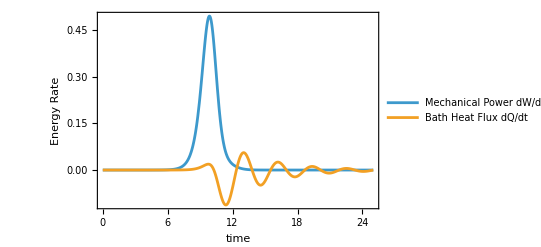

```mathematica
(*Reconstruct Phase-Space Variances Sigma_xx(t) and Sigma_pp(t) from RDM1D Properties*)
sxx[obj_,t_]:=1/(4*obj["RealShape"][t]);
spp[obj_,t_]:=Module[
{ra=obj["RealShape"][t],
ia=obj["ImaginaryShape"][t],
th=obj["Decoherence"][t]},
hbar^2*(2*th+ra+ia^2/ra)];
(*Instantaneous Internal Energy U(t)= <H(t)>*)
internalEnergy[obj_,t_]:=Module[
{xt=obj["PositionCenter"][t],
pt=obj["MomentumCenter"][t]},
(pt^2+spp[obj,t])/(2*m)+v2Ramp[t]*(xt^2+sxx[obj,t])];
(*Instantaneous Work Rate dW/dt and Heat Flux dQ/dt*)
workRate[obj_,t_]:=Module[{
xt=obj["PositionCenter"][t]},
v2Ramp'[t]*(xt^2+sxx[obj,t])];
heatRate[obj_,t_]:=Module[
{pt=obj["MomentumCenter"][t]},
gammaRamp[t]*(kTRamp[t]-(pt^2+spp[obj,t])/m)];
(*Plot Instantaneous Power (dW/dt) and Heat Flux (dQ/dt) During Transition*)
Plot[{workRate[rdmCL,t],heatRate[rdmCL,t]},{t,tMin,tMax/2},PlotRange->All,PlotLegends->{"Mechanical Power dW/dt","Bath Heat Flux dQ/dt"},Frame->True, FrameLabel->{"time","Energy Rate"},BaseStyle->FontSize->12]
```

Numerically integrating both rates across the simulation interval confirms that the sum of the integrated mechanical work ⟨W⟩ and dissipated heat ⟨Q⟩ matches the net internal energy change Δ U=U(t_max)-U(0) to high numerical precision, satisfying the First Law of Quantum Thermodynamics and recovering the exact classical equipartition difference Δ U=k_B Δ T.

```mathematica
(*Integrate Over[tMin,tMax] to Verify the First Law:Delta U=W+Q*)
totalWork=NIntegrate[workRate[rdmCL,t],{t,tMin,tMax}];
totalHeat=NIntegrate[heatRate[rdmCL,t],{t,tMin,tMax}];
deltaU=internalEnergy[rdmCL,tMax]-internalEnergy[rdmCL,tMin];
(*Exact Equipartition Difference:U(tMax)-U(0)=kT_F-kT_I*)
exactDeltaU=kTF-kTI;
Print["Integrated Mean Work <W>          = ",totalWork];
Print["Integrated Mean Heat <Q>          = ",totalHeat];
Print["Sum <W> + <Q>                     = ",totalWork+totalHeat];
Print["Actual Internal Energy Change dU  = ",deltaU];
Print["Exact Equipartition Change (kTF - kTI) = ",exactDeltaU];
Print["First Law Residual |dU - (W + Q)| = ",Abs[deltaU-(totalWork+totalHeat)]];
```

Integrated Mean Work <W>          = 0.916887

Integrated Mean Heat <Q>          = -0.116886

Sum <W> + <Q>                     = 0.800001

Actual Internal Energy Change dU  = 0.800001

Exact Equipartition Change (kTF - kTI) = 4/5

First Law Residual |dU - (W + Q)| = 2.34244×10^-9

The results above confirm the First Law of (Quantum) Thermodynamics (Δ U = ⟨W⟩ + ⟨Q⟩) to within a numerical residual of 2.34×10^-9. Because the Caldeira–Leggett master equation obeys classical equipartition at stationary thermal equilibrium  (U_eq=k_B T), increasing the bath thermal energy from 4/5 to 8/5 requires a net internal energy increase of ΔU=k_B Δ T=4/5. 

Notably, although the bath is heated to twice its initial temperature, the net integrated heat exchange is negative ⟨Q⟩=-0.116886: the rapid fourfold stiffening of the harmonic trap around t_0=10 injects ⟨W⟩=+0.916887 of mechanical compression work—exceeding the target equilibrium energy difference ΔU=4/5 and transiently overheating the oscillator’s kinetic degree of freedom above the instantaneous bath temperature. The extra 0.116886 of irreversible mechanical work is subsequently dissipated into the thermal reservoir as friction damps the breathing oscillations onto the final equilibrium plateau.

Finally, we evaluate the quantum purity and instantaneous entropy rates of the system and surrounding reservoir to verify the Second Law of (Quantum) Thermodynamics (ΔS_univ=ΔS_sys+ΔS_surr>=0). Because a Gaussian reduced density matrix is completely characterized by its second-moment covariance matrix, its quantum purity

𝒫(t)=Tr((ρ̂(t))^2)=√((Re(α_t))/(Re(α_t)+2 θ_t))

and thermodynamic Rényi-2 system entropy S_sys(t)=-ln 𝒫(t) can be tracked analytically along the numerical trajectory. Differentiating S_sys(t) and substituting the Caldeira–Leggett equations of motion yields an exact algebraic expression (see GWPEngineRDM1D appendix) for the instantaneous system entropy rate in which the unitary chirp terms cancel identically:

(Ṡ)_sys(t)=-γ(t)+(γ(t)m k_B T(t))/(ℏ^2(Re(α_t)+2 θ_t))

Combining this with reversible Clausius entropy flux exported to the surroundings

(Ṡ)_surr(t)=-(Q̇(t))/(k_B T(t))

yields the instantaneous total entropy production rate of the universe

(Ṡ)_univ(t)=(Ṡ)_sys(t)+(Ṡ)_surr(t)≥0

At thermal equilibrium in the high-temperature Caldeira–Leggett regime, the purity reduces to the ratio of the trap quantum to the thermal energy, 𝒫_eq=(ℏ ω)/(2 k_B T). Because our protocol doubles both the trap frequency (ω_f/ω_i=2) and the bath temperature (T_f/T_i=2), mechanical spatial compression exactly compensates thermal momentum broadening, resulting in iso-entropic equilibrium endpoints where 𝒫(0)=𝒫(50)=0.3125. During the finite-time ramp around t_0=10, however, the open oscillator lags behind the instantaneous Gibbs state, causing 𝒫(t) to dip transiently before recovering to 0.3125 (whereas the isolated unitary purity remains strictly frozen at all times).

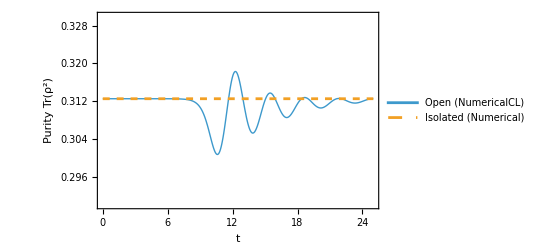

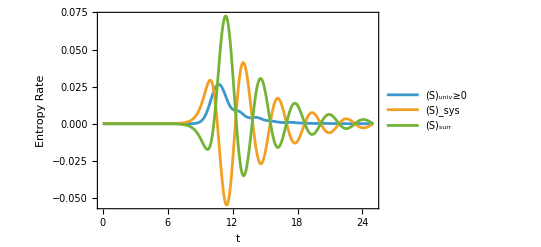

```mathematica
(*Quantum Purity Tr[rho^2] and System Entropy S_sys(t)=-Log[Purity(t)]*)purity[obj_,t_]:=Module[{ra=obj["RealShape"][t],th=obj["Decoherence"][t]},Sqrt[ra/(ra+2*th)]];
entropySys[obj_,t_]:=-Log[purity[obj,t]];
(*Exact Algebraic System Entropy Rate dS_sys/dt*)
entropyRateSys[obj_,t_]:=Module[{ra=obj["RealShape"][t],th=obj["Decoherence"][t]},-gammaRamp[t]+(gammaRamp[t]*m*kTRamp[t])/(hbar^2*(ra+2*th))];
(*Surroundings Entropy Rate:dS_surr/dt=-(dQ/dt)/kT(t)*)
entropyRateSurr[obj_,t_]:=-heatRate[obj,t]/kTRamp[t];
(*Total Universe Entropy Production Rate:dS_univ/dt=dS_sys/dt+dS_surr/dt>=0*)
entropyRateUniv[obj_,t_]:=entropyRateSys[obj,t]+entropyRateSurr[obj,t];

(*Plot Purity and Entropy Rates*)
Plot[{
purity[rdmCL,t],
purity[rdmUnitary,t]},{t,tMin,tMax/2},PlotStyle->{Thick,Dashed},PlotRange->{.29,.33},PlotLegends->{"Open (NumericalCL)","Isolated (Numerical)"},Frame->True,FrameLabel->{"t","Purity Tr(ρ^2)"},BaseStyle->FontSize->12]

Plot[{
entropyRateUniv[rdmCL,t],
entropyRateSys[rdmCL,t],
entropyRateSurr[rdmCL,t]},{t,tMin,tMax/2},PlotRange->All,PlotLegends->{"(Ṡ)_univ≥0","(Ṡ)_sys","(Ṡ)_surr"},Frame->True,FrameLabel->{"t","Entropy Rate"},BaseStyle->FontSize->12]
```

Integrating the entropy fluxes across the interval 0 to 50 confirms the Second Law of (Quantum) Thermodynamics.  Because the initial and final equilibrium states share the identical purity 𝒫(0)=𝒫(50)=0.3125, the net change in the state function S_sys vanishes up to the tiny residual relaxation tail at t_max=50 (ΔS_sys=4.05×10^-7). Meanwhile, as the excess mechanical compression work (⟨Q⟩=-0.116886) is dissipated into the reservoir, the surroundings absorb a net entropy increase of ΔS_surr=+0.0686707. Thus, all irreversible entropy generated during the finite-time transition is exported to the thermal bath, yielding a strictly positive total entropy production for the universe of ΔS_univ=ΔS_sys+ΔS_surr=+0.0686711>0.

```mathematica
(*Integrate to Verify the Second Law:Delta S_univ=Delta S_sys+Delta S_surr>=0*)deltaSsys=entropySys[rdmCL,tMax]-entropySys[rdmCL,tMin];
deltaSsurr=NIntegrate[entropyRateSurr[rdmCL,t],{t,tMin,tMax}];
deltaSuniv=deltaSsys+deltaSsurr;

Print["Initial Purity P(0) vs Final Purity P(tMax) = ",{purity[rdmCL,tMin],purity[rdmCL,tMax]}];
Print["System Entropy Change Delta S_sys           = ",deltaSsys];
Print["Surroundings Entropy Change Delta S_surr    = ",deltaSsurr];
Print["Total Universe Entropy Change Delta S_univ  = ",deltaSuniv," (>= 0, Second Law Verified!)"];
```

Initial Purity P(0) vs Final Purity P(tMax) = {0.3125,0.3125}

System Entropy Change Delta S_sys           = 4.0469×10^-7

Surroundings Entropy Change Delta S_surr    = 0.0686707

Total Universe Entropy Change Delta S_univ  = 0.0686711 (>= 0, Second Law Verified!)

## Theoretical Background

This section simply documents the equations of motion solved by the GWPNumerical package.  Further details can be found in the .nb files in the Notebooks directory of the GWPTools distribution.  Eventually, this information will make its way into the Documentation Center files for GWPTools.

### 1D GWP Equations of Motion

A generalized 1D GWP is given by

ψ(x,t)=((2Re(α_0))/π)^(1/4)ⅇ^(1/ℏ Im(γ_0))exp(-(α_t(x-x_t))^2+ⅈ/ℏ p_t(x-x_t)+ⅈ/ℏ γ_t)

where α_t is a complex-valued shape parameter, x_t and p_t are the position and momentum centers, respectively, and γ_t is a complex-valued phase.

The GWP is an exact solution of the time-dependent Schrödinger equation for a particle of mass m subject to a quadratic external potential field

V(x,t)=V_0(t)+V_1(t)x+V_2(t)x^2

GWPNumerical1D uses NDSolveValue to simultaneously integrate the six coupled first-order real ODEs for the GWP parameters from a given set of initial conditions:

(ẋ)_t=p_t/m

(ṗ)_t=-V_1(t)-2V_2(t)x_t

Re((α̇)_t)=(4ℏ)/m Re(α_t)Im(α_t)

Im((α̇)_t)=-(2ℏ)/m((Re(α_t))^2-(Im(α_t))^2)+(V_2(t))/ℏ

Re((γ̇)_t)=p_t^2/(2m)-(V_0(t)+V_1(t)x_t+V_2(t)x_t^2)-ℏ^2/m Re(α_t)

Im((γ̇)_t)=-ℏ^2/mIm(α_t)

### 1D Multi-component GWP superposition states

By the linearity of the time-dependent Schrödinger equation, a coherent superposition of N Gaussian wavepackets

ψ(x,t)=∑_(k=1)^N c_k ψ_k(x,t)

evolves such that each individual Gaussian wavepacket ψ_k(x,t) follows the six-equation system (above) independently from its own initial condition.

For GWPNumericalSS1D, the number of states is fixed N=2, and the engine simultaneously integrates the 6×2=12 coupled ODEs for wavepackets 1 and 2 in a single NDSolveValue call.  The code then dynamically reconstructs the parameters for the interference cross-terms (i.e., the component overlaps, which are also GWPs) at a given time t.  

For GWPNumericalMC1D, the number of states is determined by the user’s input, and the engine dynamically constructs and integrates the 6N ODE system for all N states and then populates the upper-triangle N(N+1)/2 packed parameter bus for the component overlaps.

### 2D GWP Equations of Motion

In two dimensions, the GWP ansatz is expressed as:

Ψ(r,t)=N exp(-(r-r_t)^TA_t(r-r_t)+ⅈ/ℏ p_t^T(r-r_t)+ⅈ/ℏ γ_t)

where r=(x,y)^T is the coordinate vector, r_t=(x_t,y_t)^T and p_t=(p_(x,t),p_(y,t))^T are the classical position and momentum vectors, γ_t is the complex-valued spatially independent phase. The geometry and phase curvature of the packet are governed by the two-by-two complex shape matrix

A_t=Re(A_t)+ⅈ Im(A_t)=(α_(x x,t) | α_(x y,t)
α_(x y,t) | α_(y y,t))

parameterized by six real functions: the real and imaginary components of α_(x x,t), α_(y y,t), and α_(x y,t).

We consider a general-2D quadratic potential surface

V(x,y,t)=V_00(t)+V_10(t)x+V_01(t)y+V_20(t)x^2+V_02(t)y^2+V_11(t)x y

with time-dependent coefficients.

GWPNumerical2D integrates the 12 coupled real ODEs for the shape matrix, the classical trajectory, and the real and imaginary components of the spatially independent phase.

The 2D classical trajectory equations of motion are

(ẋ)_t=(p_(x,t))/m

(ẏ)_t=(p_(y,t))/m

(ṗ)_(x,t)=-V_10(t)-2V_20(t)x_t-V_11(t)y_t

(ṗ)_(y,t)=-V_01(t)-2V_02(t)y_t-V_11(t)x_t

For the real component of the shape matrix, we have

Re((α̇)_(x x,t))=(4ℏ)/m(Re(α_(x x,t))Im(α_(x x,t))+Re(α_(x y,t))Im(α_(x y,t)))

Re((α̇)_(y y,t))=(4ℏ)/m(Re(α_(y y,t))Im(α_(y y,t))+Re(α_(x y,t))Im(α_(x y,t)))

Re((α̇)_(x y,t))=(2ℏ)/m(Re(α_(x x,t))Im(α_(x y,t))+Re(α_(x y,t))Im(α_(y y,t))+Im(α_(x x,t))Re(α_(x y,t))+Im(α_(x y,t))Re(α_(y y,t)))

For the imaginary “chirp” matrix components, we have

Im((α̇)_(x x,t))=-(2ℏ)/m((Re(α_(x x,t)))^2+(Re(α_(x y,t)))^2-(Im(α_(x x,t)))^2-(Im(α_(x y,t)))^2)+1/ℏ V_20(t)

Im((α̇)_(y y,t))=-(2ℏ)/m((Re(α_(y y,t)))^2+(Re(α_(x y,t)))^2-(Im(α_(y y,t)))^2-(Im(α_(x y,t)))^2)+1/ℏ V_02(t)

Im((α̇)_(x y,t))=-(2ℏ)/m(Re(α_(x y,t))(Re(α_(x x,t))+Re(α_(yy,t)))-Im(α_(x y,t))(Im(α_(x x,t))+Im(α_(y y,t))))+1/(2ℏ)V_11(t)

Finally, for the global phase, we have

Re((γ̇)_t)=1/(2m)(p_(x,t)^2+p_(y,t)^2)-V(x_t,y_t,t)-ℏ^2/m(Re(α_(x x,t))+Re(α_(y y,t)))

Im((γ̇)_t)=-ℏ^2/m(Im(α_(x x,t))+Im(α_(y y,t)))

### 1D GWP Equations of Motion for the Reduced Density Matrix

For open quantum systems governed by the CL master equation

(∂ρ)/(∂t)=-ⅈ/ℏ (-ℏ^2/(2m)((∂^2 ρ)/(∂x^2)-(∂^2 ρ)/(∂x^(′2)))+(V(x,t)-V(x',t))ρ)-1/2 γ_d(x-x')((∂ρ)/(∂x)-(∂ρ)/(∂x'))-(m γ_d k_B T(t))/ℏ^2(x-x')^2 ρ

the GWP ansatz for the reduced density matrix is given by

ρ(x,x',t)=exp(-Re(α_t)((x-x_t)^2+(x'-x_t)^2)+ⅈ Im(α_t)((x-x_t)^2-(x'-x_t)^2)-(θ_t(x-x'))^2+ⅈ/ℏ p_t(x-x')+2Re(γ_t))

which introduces a new real-valued thermal decoherence parameter θ_t>0.

Directly integrating the spatial density matrix parameters produces stiff nonlinear differential equations that can become numerically unstable during rapid thermal or mechanical ramps.  Instead, GWPNumericalRDM1D implements a three-stage linear covariance pipeline described below.

A key feature of this numerical protocol is that the friction coefficient γ_d(t) and thermal energy k_B T(t) are specified as callable functions of time rather than static scalars. Allowing simultaneous time dependence across the mechanical trap curvature V_2(t) and the environmental coupling parameters makes it possible to model arbitrary non-equilibrium thermodynamic protocols, while the underlying linear covariance formulation guarantees that rapid variations in γ_d(t) and k_B T(t) are integrated smoothly without numerical stiffness.

Stage (1) Pre-integration mapping:  The initial parameters for the shape and decoherence are mapped to the initial phase-space covariance elements of the Σ-matrix:

Σ_xx(0)=1/(4Re(α_0))

Σ_pp(0)=ℏ^2(2 θ_0+Re(α_0)+(Im(α_0))^2/(Re(α_0)))

Σ_xp(0)=(ℏ Im(α_0))/(2Re(α_0))

Stage (2) Linear Fokker-Planck ODE integration: The five ODEs for the classical trajectory and covariance matrix components are strictly linear

(ẋ)_t=p_t/m

(ṗ)_t=-V_1(t)-2V_2(t)x_t-γ_d(t)p_t

(Σ̇)_(x x)=2/m Σ_(x p)

(Σ̇)_(p p)=-4V_2(t)Σ_(x p)-2γ_d(t)Σ_(p p)+2m γ_d(t)k_B T(t)

(Σ̇)_(x p)=1/m Σ_(p p)-2V_2(t)Σ_(x x)-γ_d(t)Σ_(x p)

and can be directly integrated with NDSolveValue.

Stage (3) Post-integration reconstruction:  The interpolated variances at time t are used to algebraically reconstruct the shape and decoherence parameters and the real phase

Re(α_t)=1/(4Σ_(x x)(t))

Im(α_t)=(Σ_(x p)(t))/(2ℏ Σ_(x x)(t))

θ_t=(Σ_(x x)(t)Σ_(p p)(t)-(Σ_(x p)(t))^2)/(2 ℏ^2 Σ_(x x)(t))-1/(8Σ_(x x)(t))

Re(γ_t)=1/4 ln((2Re(α_t))/π)